```mathematica
temperature=Import["C:\\Users\\Расим\\Desktop\\temperature.txt","Table"];
x=Import["C:\\Users\\Расим\\Desktop\\temperature1.txt","Table"];
y=Import["C:\\Users\\Расим\\Desktop\\temperature2.txt","Table"];
```

```mathematica
temp=Table[{x[[n,1]],y[[n,1]],temperature[[n,1]]},{n,1,Length[x]}];
```

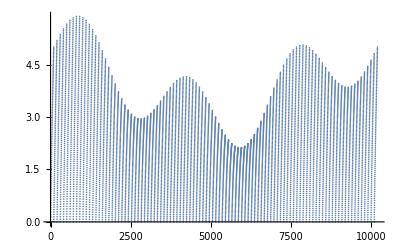

```mathematica
ListPlot[temp[[All,3]]]
```

```mathematica
ListPlot3D[temp]
```

-Graphics3D-

Function[r,(∑_(n=1)^300 ((-1)^(n+1) Sin[n π r])/n)/r]

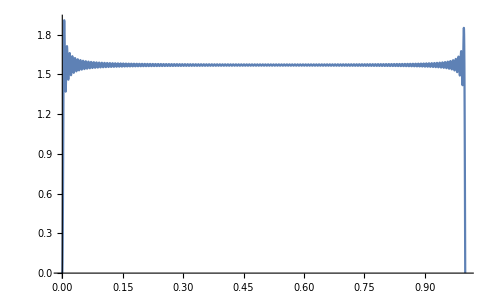

```mathematica
u=Function[r,Sum[(-1)^(n+1)/n*Sin[n*Pi*r],{n,1,300}]/r]

Plot[u[r],{r,0,1},PlotRange->All]
```

```mathematica
NDSolve[{Laplacian[fun[x2,y2],{x2,y2},"Polar"]==0,DirichletCondition[fun[x2,y2]==2+Sin[3*y2],True]},fun,{x2,y2}∈Disk[]]
Plot3D[Evaluate[fun[x2,y2]/.%],{x2,y2}∈Disk[]]
```

{{fun→InterpolatingFunction[…]}}

-Graphics3D-